### Mass Matrix - 1 Flavour Scenario for Both sided Local Clockwork

```mathematica
K = 19;qt=0;a=1;q=-1;c=-01.0;
(* qt is q^∼ (Majorana mass term), K is the number of sites and a is mass term (m) and q and c are the neighbouring coupling strength term in CW fermions. *)
```

```mathematica
bcw = Table[0,{x,2K+1},{y,2K+1}];
(* Dummy matrix to form clockwork mass matrix *)
```

```mathematica
i=1;While[i<2K+2,{bcw[[i,i]] = qt };i++]
i=1;While[i<K+1,{bcw[[i,K+i]] = a};i++]
i=1;While[i<K+1,{bcw[[K+i,i]] = a };i++]
i=1;While[i<K+1,{bcw[[i,K+1+i]] = q};i++]
i=1;While[i<K+1,{bcw[[K+1+i,i]] = q};i++]
i=1;While[i<K,{bcw[[i+1,K+i]] = c};i++]
i=1;While[i<K,{bcw[[K+i,i+1]] = c};i++]
(* Clockwork mass matrix in Ψ basis, where Ψ = ( Subscript[ψ, L,0],Subscript[ψ, L,1],Subscript[ψ, L,2], ..... Subscript[ψ, L,K-1],Subscript[ψ^c, R,0],Subscript[ψ^c, R,1], .... Subscript[ψ^c, R,K] *)
```

```mathematica
bcw;
```

```mathematica
cw3 = bcw[[1;;K,K+1;;2K+1]]
```

(1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1. | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1. | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1. | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1. | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1. | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1. | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1. | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 1 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 1 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 1 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 1 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 1 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 1 | -1)

```mathematica
NullSpace[cw3]
```

(0.267261 | 0.267261 | 3.04068×10^-16 | -0.267261 | -0.267261 | -3.75183×10^-16 | 0.267261 | 0.267261 | 4.43025×10^-16 | -0.267261 | -0.267261 | -6.66016×10^-16 | 0.267261 | 0.267261 | 9.22996×10^-16 | -0.267261 | -0.267261 | -9.34324×10^-16 | 0.267261 | 0.267261)

```mathematica
%[[-1]][[-1]]
```

0.267261

```mathematica
ns =NullSpace[bcw]
```

(1.94289×10^-16 | 9.71445×10^-17 | -1.66533×10^-16 | -2.77556×10^-16 | 6.93889×10^-18 | 8.32667×10^-17 | 4.996×10^-16 | 1.38778×10^-16 | -9.02056×10^-17 | -4.02456×10^-16 | -3.81639×10^-16 | -1.38778×10^-16 | 9.71445×10^-17 | 1.66533×10^-16 | 8.32667×10^-17 | -1.64944×10^-28 | -6.93889×10^-17 | -2.35922×10^-16 | -2.22046×10^-16 | -0.267261 | -0.267261 | -4.09298×10^-17 | 0.267261 | 0.267261 | 1.13414×10^-16 | -0.267261 | -0.267261 | -2.54674×10^-16 | 0.267261 | 0.267261 | 1.62882×10^-16 | -0.267261 | -0.267261 | -4.72986×10^-17 | 0.267261 | 0.267261 | -6.74865×10^-18 | -0.267261 | -0.267261)

```mathematica
%[[-1]][[-1]]
```

-0.267261

```mathematica
Kcw = bcw[[1;;K,K+1;;2K+1]];
```

```mathematica
{s1,s2,s3}=SingularValueDecomposition[N[Kcw,30]];
```

```mathematica
ev = Eigenvalues[bcw]
```

{-2.97589,2.97589,-2.90416,2.90416,2.78662,-2.78662,2.62621,-2.62621,2.42699,-2.42699,2.19403,-2.19403,-1.93338,1.93338,-1.65203,1.65203,1.35827,-1.35827,1.06475,-1.06475,0.975855,-0.975855,0.907568,-0.907568,0.812759,-0.812759,-0.750014,0.750014,0.632792,-0.632792,-0.502635,0.502635,-0.401935,0.401935,0.256436,-0.256436,0.135893,-0.135893,-6.81913×10^-17}

```mathematica
Y = Eigenvectors[bcw];
```

```mathematica
H= Inverse[Y];
```

```mathematica
Ev1 = Sort[Abs[ ev]];
```

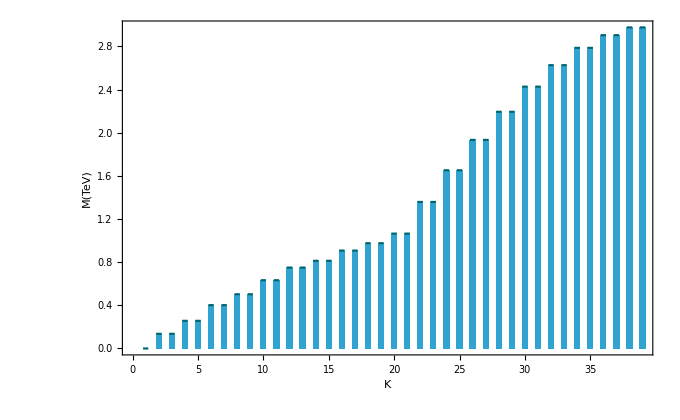

```mathematica
DiscretePlot[Ev1⟦i⟧,{i,1,2 K+1},PlotStyle->Directive[RGBColor[0.,0.4,0.42],Opacity[1.],AbsoluteThickness[1.545]],ExtentSize->0.4,ImageSize->680,BaseStyle->{FontFamily->"LM Roman 10",FontSize->10},Frame->True,Filling->Axis,FillingStyle->Opacity[0.9,RGBColor[0.1,0.6,0.8]],FrameTicks->{Automatic,Automatic},FrameLabel->{"K","M(TeV)"},LabelStyle->Directive[Bold,Medium],PlotRange->{0,All}, Epilog->{Text[ "",Scaled[{0.8,0.95}]],Text["",Scaled[{0.8,0.9}]]}]
```

```mathematica
Rn = H[[2K+1,All]] 
(* Change of basis from Subscript[ψ^c, R,r]  to eigenvector of BCW in interaction term. *)
```

{-0.0146628,-0.0146628,-0.0296304,0.0296304,-0.0452392,-0.0452392,-0.0618971,0.0618971,-0.0801431,-0.0801431,-0.100752,0.100752,-0.124939,0.124939,0.154822,-0.154822,0.194706,-0.194706,0.256038,-0.256038,-0.0135714,-0.0135714,0.0765861,-0.0765861,-0.231713,0.231713,0.193587,0.193587,0.100111,-0.100111,-0.294964,0.294964,0.0594299,0.0594299,-0.279159,-0.279159,-0.148292,0.148292,0.267261}

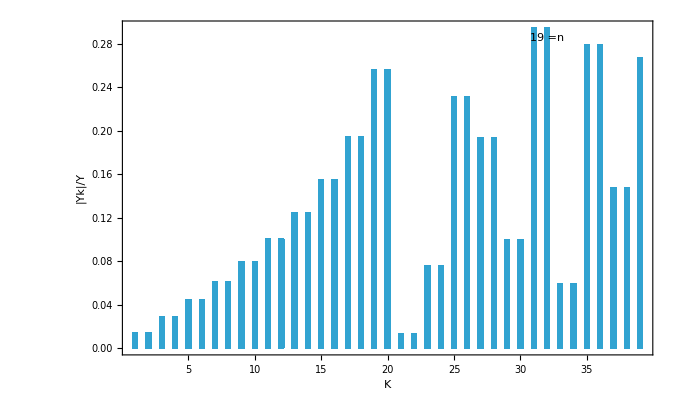

```mathematica
DiscretePlot[Abs[Rn[[i]]],{i,1,2*K+1},ExtentSize->0.4,ImageSize->680,BaseStyle->{FontFamily->"LM Roman 10",FontSize->10},Frame->True,PlotStyle-> {Opacity[0.9,RGBColor[0.1,.6,.8]],Directive[AbsoluteThickness[0]]},
Filling->Axis,FillingStyle->Opacity[0.9,RGBColor[0.1,.6,.8]],FrameTicks->{Automatic,Automatic},FrameLabel->{"K","|Yk|/Y"},LabelStyle->Directive[Bold, Medium],Epilog->{Text["",Scaled[{0.8,0.90}]],Text["",Scaled[{0.8,0.95}]],{Text[K"=n",Scaled[{.8,.95}]]}}]
```

```mathematica
Lvector = Transpose[s1]; (*Left Eigenvector of BCW*)
Rvector= Transpose[s3];(*Right Eigenvector of BCW*)
```

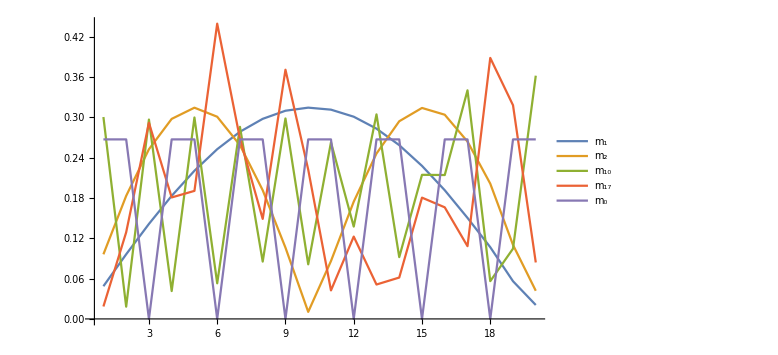
-Graphics-Absolute value of eigenvector componentsSite

```mathematica
Labeled[Labeled[ListLinePlot[{Abs[Rvector[[1]]],Abs[Rvector[[2]]],Abs[Rvector[[10]]],Abs[Rvector[[17]]],Abs[Rvector[[-1]]]},PlotRange->All,PlotLegends->Placed[LineLegend[ColorData[97]/@Range[Length[Rvector]],(*Explicit colors*){"\!\(\*SubscriptBox[\(m\), \(1\)]\)","\!\(\*SubscriptBox[\(m\), \(2\)]\)","\!\(\*SubscriptBox[\(m\), \(10\)]\)","m_17","\!\(\*SubscriptBox[\(m\), \(0\)]\)"}]//Framed[#,FrameStyle->Black,RoundingRadius->5,Background->White]&,Right],AxesLabel->{None,None},PlotRange->All,ImageSize->Large,PlotStyle->ColorData[97]/@Range[Length[Rvector]]],Style[Rotate["Absolute value of eigenvector components",90 Degree],14],Left],Style["Site",14],Bottom]
```

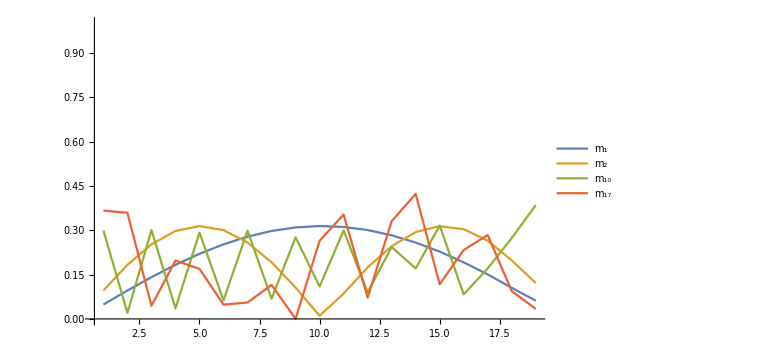
-Graphics-Absolute value of eigenvector componentsSite

```mathematica
Labeled[Labeled[ListLinePlot[{Abs[Lvector[[1]]],Abs[Lvector[[2]]],Abs[Lvector[[10]]],Abs[Lvector[[17]]]},PlotRange->{All,{0,1}},PlotLegends->Placed[LineLegend[ColorData[97]/@Range[Length[Rvector]],(*Explicit colors*){"\!\(\*SubscriptBox[\(m\), \(1\)]\)","\!\(\*SubscriptBox[\(m\), \(2\)]\)","\!\(\*SubscriptBox[\(m\), \(10\)]\)","m_17"}]//Framed[#,FrameStyle->Black,RoundingRadius->5,Background->White]&,Right],AxesLabel->{None,None},PlotRange->All,ImageSize->Large,PlotStyle->ColorData[97]/@Range[Length[Rvector]]],Style[Rotate["Absolute value of eigenvector components",90 Degree],14],Left],Style["Site",14],Bottom]
```

### 3 Flavour Scenario

```mathematica
q=-2.5;K=19;v=0.173;p=v;c = -0.11;
 (*K is the number of sites parameter, p is the coupling strength between SM neutrino and Subscript[R, n], and q and c are the neighbouring coupling strength.*)
```

```mathematica
cw= Table[0,{x,K+1},{y,K+1}];
(* Dummy matrix to form clockwork mass matrix *)
```

```mathematica
i=1;
While[i<K+1,{cw[[i+1,i+1]]=1,cw[[i+1,i]]=q};i++]
i=2;
While[i<K+1,{cw[[i,i+1]]=c};i++]
cw2=cw;cw3=cw;
(* Clockwork mass matrix in Ψ basis, where Ψ = ( Subscript[ψ, L,0],Subscript[ψ, L,1],Subscript[ψ, L,2], ..... Subscript[ψ, L,K-1],Subscript[ψ^c, R,0],Subscript[ψ^c, R,1], .... Subscript[ψ^c, R,K] *)
```

```mathematica
cw[[1,1]]=4.92p;cw2[[1,1]]=5p;cw3[[1,1]]=1p;(*3 BCW chains for 3 masses.*)
```

```mathematica
cw3;
```

```mathematica
{u1,m1,v1}=SingularValueDecomposition[SetPrecision[cw,20]];{u2,m2,v2}=SingularValueDecomposition[SetPrecision[cw2,20]];{u3,m3,v3}=SingularValueDecomposition[SetPrecision[cw3,20]];
```

```mathematica
a1=m1[[-1,-1]]
a2=m2[[-1,-1]]
a3=m3[[-1,-1]](*Three Masses produced*)
```

4.9746328364170880679×10^-14

5.04562113917727676×10^-14

1.0747091294094194992×10^-14

```mathematica
(a2^2-a1^2)*Power[10,24](*Mass squared differences Subscript[Δm^2, 21].*)
(a3^2-a2^2)*Power[10,24](*Mass squared differences Subscript[Δm^2, 32].*)
```

0.000071132082295347716

-0.002430329296727664767